```mathematica
(* 标定长度单位*)
h0=1;
(* Subscript[先定义经常用到的式子和文献中给出的A, i]*)
raSinh[x_,h_,H_,x3_]:=Evaluate[D[Sinh[x*h]/Sinh[x*H],x]];
raSinh2[x_,h_,H_,x3_]:=Evaluate[D[Sinh[x*(H-x3)] Sinh[x*h]/Sinh[x*H],x]];
sh[x_,h_,H_,x3_]:=Sinh[x*h]/Sinh[x*H]Sinh[x*(H-x3)];
j0sh[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[0,√(r1^2+r2^2)2Pi*x]sh[x k,h h0,H h0,x3 h0]]];

j1xsh[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0]]];

(*For v33*)
j0xdsh[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[0,√(r1^2+r2^2)2Pi x]k x raSinh2[x k ,h h0,H h0,x3 h0]]];

(* w11 = (x^2-y^2)/ρ^3 j1xa1-x^2/ρ^2 j0x2a1 *)
j1xa1[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x]k x a1[x k ,h h0,H h0,x3 h0]]];

j0x2a1[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[0,√(r1^2+r2^2)2Pi x](k x)^2 a1[x k ,h h0,H h0,x3 h0]]];

j0a2[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[0,√(r1^2+r2^2)2Pi x]a2[x k ,h h0,H h0,x3 h0]]];

j1xa3[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x] k x a3[x k ,h h0,H h0,x3 h0]]];

j1xa4[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x] k x a4[x k ,h h0,H h0,x3 h0]]];
(* For u13.*)

j1xa4s[x_,r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x] k x a4s[x k ,h h0,H h0,x3 h0]]];
(* For u31.*)
```

```mathematica
(* 开始求导数*)
```

```mathematica
d1j0sh=D[j0sh[x, r1, r2,r3,h,H],r1];
```

```mathematica
d1j1xsh=D[r1^2/(√(r1^2+r2^2))j1xsh[x, r1, r2,r3,h,H],r1];
```

```mathematica
d1v11=d1j0sh+d1j1xsh;
d2v21=D[(r1 r2)/(√(r1^2+r2^2))j1xsh[x, r2, r1,r3,h,H],r2];
d3v31=D[(r1(x3-h))/(√(r1^2+r2^2))j1xsh[x, r1, r2,r3,h,H],r3];
```

```mathematica
Simplify[d3v31+d2v21+d1v11]
```

1/(√(r1^2+r2^2))4 π^2 r1 x Csch[2 H π x] Sinh[2 h π x] (π √(r1^2+r2^2) x (BesselJ[0,2 π √(r1^2+r2^2) x]-BesselJ[2,2 π √(r1^2+r2^2) x]) Sinh[2 π (H-r3) x]+BesselJ[1,2 π √(r1^2+r2^2) x] (2 π x (h-x3) Cosh[2 π (H-r3) x]+Sinh[2 π (H-r3) x]))

```mathematica
d1v11=D[j0sh[x, r1, r2,r3,h,H]+r1^2/(√(r1^2+r2^2))j1xsh[x, r1, r2,r3,h,H],r1];
d2v21=D[(r1 r2)/(√(r1^2+r2^2))j1xsh[x, r2, r1,r3,h,H],r2];
d3v31=D[(r1(r3-h))/(√(r1^2+r2^2))j1xsh[x, r1, r2,r3,h,H],r3];
d1w11=D[(r1^2-r2^2)/((√(r1^2+r2^2))^3)j1xa1[x, r1, r2,r3,h,H]-r1^2/(r1^2+r2^2)j0x2a1[x, r1, r2,r3,h,H],r1];
d2w21=D[(2r1 r2)/((√(r1^2+r2^2))^3)j1xa1[x, r2, r1,r3,h,H]-(r1 r2)/(r1^2+r2^2)j0x2a1[x, r2, r1,r3,h,H],r2];
d3w31=D[r1/(√(r1^2+r2^2))j1xa4s[x, r1, r2,r3,h,H],r3];
```

```mathematica
d3v31/.{r1->1,r2->2,r3->2,h->1,H->4,x->1}//N
```

-0.0122987

```mathematica
d3w31
```

(8 π^3 r1 x^2 BesselJ[1,2 π √(r1^2+r2^2) x] (-2 H (-h+H) π x Cosh[2 π r3 x] Sinh[2 h π x]+2 H π r3 x (2 h π x Cosh[2 π (-h+r3) x]-2 H π x Cosh[2 π (H-r3) x] Csch[2 H π x] Sinh[2 h π x])+r3 (2 H π x Cosh[2 π r3 x] Sinh[2 h π x]-2 h π x Cosh[2 π (-h+H-r3) x] Sinh[2 H π x])-4 h H^2 π^2 x^2 Cosh[2 π r3 x] Csch[2 H π x] Sinh[2 (-h+H) π x]+h Sinh[2 H π x] Sinh[2 π (-h+H-r3) x]+H Sinh[2 h π x] Sinh[2 π r3 x]+2 H π x (H Csch[2 H π x] Sinh[2 h π x] Sinh[2 π (H-r3) x]+h Sinh[2 π (-h+r3) x])))/(√(r1^2+r2^2) (-4 H^2 π^2 x^2+Sinh[2 H π x]^2))

```mathematica
r1
```

r1

```mathematica
NIntegrate[(d1w11+d2w21+d3w31+d1v11+d2v21+d3v31)/.{r1->1,r2->2,r3->2,h->1,H->4},{x,0,Infinity}]
```

-(8 π^3 x^2 BesselJ[1,2 √5 π x] Cosh[4 π x] Csch[8 π x] Sinh[2 π x])/(√5)+(8 π^2 x BesselJ[1,2 √5 π x] Csch[8 π x] Sinh[2 π x] Sinh[4 π x])/(√5)+4 π^3 x^2 (BesselJ[0,2 √5 π x]-BesselJ[2,2 √5 π x]) Csch[8 π x] Sinh[2 π x] Sinh[4 π x]+(8 π^3 x^2 BesselJ[1,2 √5 π x] (-24 π x Cosh[4 π x] Sinh[2 π x]+16 π x (2 π x Cosh[2 π x]-8 π x Cosh[4 π x] Csch[8 π x] Sinh[2 π x])+4 Sinh[2 π x] Sinh[4 π x]+8 π x (Sinh[2 π x]+4 Csch[8 π x] Sinh[2 π x] Sinh[4 π x])-64 π^2 x^2 Cosh[4 π x] Csch[8 π x] Sinh[6 π x]+Sinh[2 π x] Sinh[8 π x]+2 (8 π x Cosh[4 π x] Sinh[2 π x]-2 π x Cosh[2 π x] Sinh[8 π x])))/(√5 (-64 π^2 x^2+Sinh[8 π x]^2))-(8 π^3 x^2 BesselJ[0,2 √5 π x] (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(5 (-64 π^2 x^2+Sinh[8 π x]^2))+(4 π^2 x BesselJ[1,2 √5 π x] (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(5 √5 (-64 π^2 x^2+Sinh[8 π x]^2))+(16 π^4 x^3 BesselJ[1,2 √5 π x] (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(√5 (-64 π^2 x^2+Sinh[8 π x]^2))+(4 π^3 x^2 (BesselJ[0,2 √5 π x]-BesselJ[2,2 √5 π x]) (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(5 (-64 π^2 x^2+Sinh[8 π x]^2))

```mathematica
d1v12=D[(r1 r2)/(√(r1^2+r2^2))j1xsh[x, r1, r2,r3,h,H],r1];
d2v22=D[j0sh[x, r2, r1,r3,h,H]+r2^2/(√(r1^2+r2^2))j1xsh[x, r2, r1,r3,h,H],r2];
d3v32=D[(r2(r3-h))/(√(r1^2+r2^2))j1xsh[x, r2, r1,r3,h,H],r3];
d1w12=D[(2r1 r2)/((√(r1^2+r2^2))^3)j1xa1[x, r1, r2,r3,h,H]-(r1 r2)/(r1^2+r2^2)j0x2a1[x, r1, r2,r3,h,H],r1];
d2w22=D[(r2^2-r1^2)/((√(r1^2+r2^2))^3)j1xa1[x, r2, r1,r3,h,H]-r2^2/(r1^2+r2^2)j0x2a1[x, r2, r1,r3,h,H],r2];
d3w32=D[r2/(√(r1^2+r2^2))j1xa4s[x, r2, r1,r3,h,H],r3];
```

```mathematica
(* Subscript[dG^i, j]/Subscript[dx, j]*)
```

```mathematica
d1v13=D[(r1(r3-h))/(√(r1^2+r2^2))j1xsh[x, r1, r2,r3,h,H],r1];
d2v23=D[(r2(r3-h))/(√(r1^2+r2^2))j1xsh[x, r2, r1,r3,h,H],r2];
d3v33=D[j0sh[x, r1, r2,r3,h,H]-j0xdsh[x, r1, r2,r3,h,H],r3];
d1w13=D[r1/(√(r1^2+r2^2))j1xa4[x, r1, r2,r3,h,H],r1];
d2w23=D[r2/(√(r1^2+r2^2))j1xa4[x, r2, r1,r3,h,H],r2];
d3w33=D[j0a2[x, r1, r2,r3,h,H],r3];
```

```mathematica
d11 =-(8 π^3 x^2 BesselJ[1,2 √5 π x] Cosh[4 π x] Csch[8 π x] Sinh[2 π x])/(√5)+(8 π^2 x BesselJ[1,2 √5 π x] Csch[8 π x] Sinh[2 π x] Sinh[4 π x])/(√5)+4 π^3 x^2 (BesselJ[0,2 √5 π x]-BesselJ[2,2 √5 π x]) Csch[8 π x] Sinh[2 π x] Sinh[4 π x]+(8 π^3 x^2 BesselJ[1,2 √5 π x] (-24 π x Cosh[4 π x] Sinh[2 π x]+16 π x (2 π x Cosh[2 π x]-8 π x Cosh[4 π x] Csch[8 π x] Sinh[2 π x])+4 Sinh[2 π x] Sinh[4 π x]+8 π x (Sinh[2 π x]+4 Csch[8 π x] Sinh[2 π x] Sinh[4 π x])-64 π^2 x^2 Cosh[4 π x] Csch[8 π x] Sinh[6 π x]+Sinh[2 π x] Sinh[8 π x]+2 (8 π x Cosh[4 π x] Sinh[2 π x]-2 π x Cosh[2 π x] Sinh[8 π x])))/(√5 (-64 π^2 x^2+Sinh[8 π x]^2))-(8 π^3 x^2 BesselJ[0,2 √5 π x] (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(5 (-64 π^2 x^2+Sinh[8 π x]^2))+(4 π^2 x BesselJ[1,2 √5 π x] (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(5 √5 (-64 π^2 x^2+Sinh[8 π x]^2))+(16 π^4 x^3 BesselJ[1,2 √5 π x] (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(√5 (-64 π^2 x^2+Sinh[8 π x]^2))+(4 π^3 x^2 (BesselJ[0,2 √5 π x]-BesselJ[2,2 √5 π x]) (16 π x Sinh[4 π x] Sinh[6 π x]+16 π x Cosh[4 π x] (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x]) Sinh[8 π x]+2 (-4 Cosh[4 π x] Sinh[2 π x]+Cosh[2 π x] Sinh[8 π x])-4 Sinh[4 π x] (8 π x (3 Cosh[6 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[6 π x])+(Cosh[2 π x] Csch[8 π x]-4 Coth[8 π x] Csch[8 π x] Sinh[2 π x]) Sinh[8 π x])))/(5 (-64 π^2 x^2+Sinh[8 π x]^2));
```

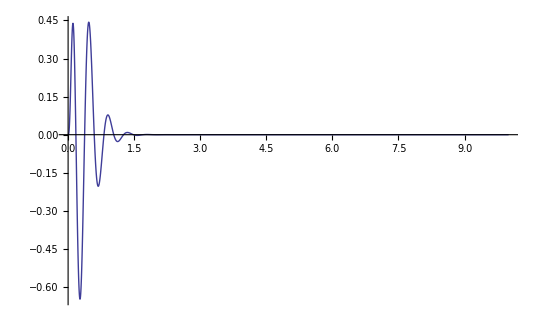

```mathematica
Plot[d11,{x,0,10},PlotRange->All]
```

```mathematica
Block[{NIntegrate, x, y},
integrand=Inactive[NIntegrate[x*y,{x,0, 1}]];
numbericalModel[y_?NumericQ]=Activate[D[integrand,y]]];
```

NIntegrate::inumr: The integrand x\ y has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

```mathematica
numbericalModel[1]
```

0.5

```mathematica
f=Inactive[NIntegrate[x*y^2,{x,0, 1}]];
g[y_?NumericQ]=Activate[D[f,y]];
```

NIntegrate::inumr: The integrand 2\ x\ y has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate::inumr: The integrand x\ y^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate::inumr: The integrand 2\ x\ y has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

```mathematica
g[1]
```

1.

```mathematica
d1dj0[r1_,r2_,x_]:=Evaluate[D[2Pi BesselJ[0,√(r1^2+r2^2)2Pi*x],r1]];
d1dj1r[r1_,r2_,x_]:=Evaluate[D[(r1^2 h0)/(√(r1^2+r2^2))2Pi BesselJ[1,√(r1^2+r2^2)2Pi x],r1]];
d2dj1r[r1_,r2_,x_]:=Evaluate[D[(r1 r2 h0)/(√(r1^2+r2^2))2Pi BesselJ[1,√(r1^2+r2^2)2Pi x],r1]];
d1j0shNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[d1dj0[r1,r2,x]sh[x k,h h0,H h0,x3 h0],{x,0,Infinity}]]]

d1j0shNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},If[x3<h+1/E,d1j0shNhNearh[r1,r2,x3,h,H],NIntegrate[d1dj0[r1,r2,x]sh[x k,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"]]]];

d1j1xshNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[d1dj1r[r1,r2,x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]];
d1j1xshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},If[x3<h+1/E,d1j1xshNhNearh[r1,r2,x3+10^-6,h,H],NIntegrate[d1dj1r[r1,r2,x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]]];
d1v11[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},d1j0shNh[##]+d1j1xshNh[##]&[r1,r2,x3,h,H]];
d2v21[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},d1j1xshNh[##]&[r1,r2,x3,h,H]];
```

```mathematica
d1v11[1,1,1.5,1,4]
```

-0.0639142

```mathematica
Clear["Global`*"]
```

```mathematica
f=NIntegrate[D[x*y^2, y],{x,0,1}]
```

NIntegrate::inumr: The integrand 2\ x\ y has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[∂_y (x y^2),{x,0,1}]

NIntegrate::inumr: The integrand 2\ x\ y has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::ivar: 3 is not a valid variable.

NIntegrate::inumr: The integrand ∂_3 (9\ x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate[∂_3 (x 3^2),{x,0,1}]

```mathematica
divV1Part1[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi x](2Pi x r1 ) (1-√(r1^2+r2^2)2Pi x)/(√(r1^2+r2^2))sh[x,h,H,x3],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]];
divV1Part2[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x](2Pi x r1 ) sh[x,h,H,x3],{x,0,Infinity}(*,Method->"ExtrapolatingOscillatory"*)]]];
```

```mathematica
divV1[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},r2^2/(r1^2+r2^2)divV1Part1[##]+(-2 r1^3)/((r1^2+r2^2)^(3/2))divV1Part2[##]&[r1,r2,x3,h,H]];
```

```mathematica
divV1Part2[1,1,2,1,5]
```

0.0118321

```mathematica
Manipulate[Plot[With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x](k x r1 h0) (1-√(r1^2+r2^2)k*h0 x)/(√(r1^2+r2^2))sh[x,h,H,x3]]/.{r1->1,r2->2,h->1,H->4,x3->x33}],{x,0,10},PlotRange->All],{x33,{1,2,3}}]
```

```mathematica
Manipulate[Plot[With[{h0=h0},With[{k=2Pi/h0},k BesselJ[1,√(r1^2+r2^2)2Pi x](2Pi x r1 ) sh[x,h,H,x3]/.{r1->1,r2->2,h->1,H->4,x3->x33}]],{x,0,10},PlotRange->All],{x33,{1,2,3}}]
```

```mathematica
divW1[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi x](2Pi x H )^3 (Sinh[h x 2Pi]Sinh[x3 x 2Pi])/(Sinh[H x 2Pi]^2(Sinh[H x 2Pi]^2-(H x 2Pi)^2)),{x,0,Infinity}]]];
```

```mathematica
divW1[1, 1, 0.1, 1,4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {5.01188×10^-9}. NIntegrate obtained 0.0858044 and 0.00391603 for the integral and error estimates.

0.0858044

```mathematica
Manipulate[Plot[With[{h0=h0},With[{k=2Pi/h0},k BesselJ[0,√(r1^2+r2^2)2Pi x](2Pi x H )^4 (Sinh[h x 2Pi]Sinh[x3 x 2Pi])/(Sinh[H x 2Pi]^2(Sinh[H x 2Pi]^2-(H x 2Pi)^2))/.{r1->10,r2->1,h->1,H->4,x3->x33}]],{x,0,1},PlotRange->All],{x33,{1,2,3}}]
```

```mathematica
Series[Sinh[H x 2Pi]^2(Sinh[H x 2Pi]^2-(H x 2Pi)^2),{x,0,10}]
```

64/3 H^6 π^6 x^6+1792/45 H^8 π^8 x^8+31744/945 H^10 π^10 x^10+O[x]^11

```mathematica
Series[Sinh[h x 2Pi]Sinh[x3 x 2Pi](2Pi x H )^3 BesselJ[0,√(r1^2+r2^2)2Pi x],{x,0,10}]
```

32 h H^3 π^5 x3 x^5+32/3 H^3 π^3 (2 h^3 π^4 x3-3 h π^4 r1^2 x3-3 h π^4 r2^2 x3+2 h π^4 x3^3) x^7+8 H^3 π^3 (2 π ((4 h^5 π^5)/15+1/2 h π^5 (r1^2+r2^2)^2+4/3 h^3 π^3 (-π^2 r1^2-π^2 r2^2)) x3+4/3 π^3 ((4 h^3 π^3)/3+2 h π (-π^2 r1^2-π^2 r2^2)) x3^3+8/15 h π^6 x3^5) x^9+O[x]^11

-4 H^2 π^2 x^2+Sinh[2 H π x]^2

```mathematica
j0xchNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi*x](k x)ch[x k,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"]]];
j1xa3Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi*x](k x)a3[x k,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"]]];
j1xshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]];
```

```mathematica
diff[r1_,r2_,x3_,h_,H_]:=r1 *j0xchNh[##]+r1/(√(r1^2+r2^2))j1xa3Nh[##]-(x3-h)r1/(√(r1^2+r2^2))j1xshNh[##]&[r1,r2,x3,h,H]
```

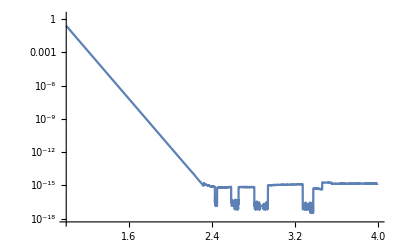

```mathematica
LogPlot[Abs[diff[1,1,x3,1,4]],{x3,1,4},PlotRange->All]
```

```mathematica
diff[1,1,2,1,4]
```

-0.161132

```mathematica
diff[1,1,1.3,1,4]
```

1.36726×10^-9

```mathematica
BesselJ[0,0]*Sinh[2 0]/Sinh[4 0]
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Indeterminate

```mathematica
Limit[Sinh[2 x]/Sinh[4 x],x->0]
```

1/2

```mathematica
Integrate[BesselJ[0,x]Tanh[x],{x,0,Infinity}]
```

∫_0^∞ BesselJ[0,x] Tanh[x]ⅆx

```mathematica
NIntegrate[BesselJ[0,x]Tanh[x],{x,0,Infinity}]
```

0.400738

```mathematica
10^9/3600/24/24/10
```

15625/324

```mathematica
N[15625/324]
```

48.2253

```mathematica
N[312500/27]
```

```mathematica
11574.074074074075/365
```

31.7098

```mathematica
Rationalize[31.70979198376459]
```

62500/1971

```mathematica
10000^2*10/3600/24/24
```

78125/162

```mathematica
N[78125/162]
```

482.253

```mathematica
N[15625/324]
```

48.2253

```mathematica
N[125/108]
```

1.15741

```mathematica
dr = 10^-4;
```

```mathematica
u11Nh[4.18072045,1.61116966,0.6142471,1,4]
```

0.0218512

```mathematica
u21Nh[4.18072045,1.61116966,0.6142471,1,4]
```

0.0162643

```mathematica
u31Nh[4.18072045,1.61116966,0.6142471,1,4]
```

0.000864592

```mathematica
d1u11 =(u11Nh[4.18072045+dr,1.61116966,0.6142471,1,4]-u11Nh[4.18072045-dr,1.61116966,0.6142471,1,4])/(2dr)
```

-0.0078635

```mathematica
d2u21=(u12Nh[1,2+dr,2,1,4]-u12Nh[1,2-dr,2,1,4])/(2dr)
```

-0.0554435

```mathematica
d3u31=(u31Nh[1,2,2+dr,1,4]-u31Nh[1,2,2-dr,1,4])/(2dr)
```

0.00926237

```mathematica
Ndiv1[x_,y_,z_]:=Module[{a,b,c},
a=(u11Nh[x+dr,y,z,1,4]-u11Nh[x-dr,y,z,1,4])/(2dr);b=(u12Nh[x,y+dr,z,1,4]-u12Nh[x,y-dr,z,1,4])/(2dr);c=(u31Nh[x,y,z+dr,1,4]-u31Nh[x,y,z-dr,1,4])/(2dr);Print["a=",a," b=", b," c=",c];Print[a+b+c]];
Ndiv3[x_,y_,z_]:=Module[{a,b,c},
a=(u13Nh[x+dr,y,z,1,4]-u13Nh[x-dr,y,z,1,4])/(2dr);b=(u23Nh[x,y+dr,z,1,4]-u23Nh[x,y-dr,z,1,4])/(2dr);c=(u33Nh[x,y,z+dr,1,4]-u33Nh[x,y,z-dr,1,4])/(2dr);Print["a=",a," b=", b," c=",c];Print[a+b+c]];
ux[x_,y_,z_]:=Module[{a,b,c},
a=u11Nh[x,y,z,1.,4.];b=u21Nh[x,y,z,1.,4.];c=u31Nh[x,y,z,1.,4.];Print["u11=",a," u21=", b," u31=",c]];
uy[x_,y_,z_]:=Module[{a,b,c},
a=u12Nh[x,y,z,1.,4.];b=u22Nh[x,y,z,1.,4.];c=u32Nh[x,y,z,1.,4.];Print["u12=",a," u22=", b," u32=",c]];
uz[x_,y_,z_]:=Module[{a,b,c},
a=u13Nh[x,y,z,1.,4.];b=u23Nh[x,y,z,1.,4.];c=u33Nh[x,y,z,1.,4.];Print["u13=",a," u23=", b," u33=",c]];
```

```mathematica
Ndiv1[-0.98487777,0.32490184,1.82523161]
```

a=0.0818284 b=-0.180657 c=0.0988287

-2.46719×10^-9

```mathematica
Ndiv3[-0.98487777,0.32490184,1.82523161]
```

a=-0.147007 b=0.0827322 c=0.0642746

1.463×10^-9

```mathematica
Ndiv3[9.84499415,-9.97181441,0.56359101]
```

a=2.68902×10^-8 b=2.7693×10^-8 c=-5.45848×10^-8

-1.54671×10^-12

```mathematica
u33Nh[4.18072045,1.61116966,1.1+dr,1,4]-u33Nh[4.18072045,1.61116966,1.1-dr,1,4]
```

-7.53996×10^-6

```mathematica
ux[-0.98487777+dr,0.32490184,1.82523161]//N
uy[-0.98487777+dr,0.32490184,1.82523161]
uz[-0.98487777+dr,0.32490184,1.82523161]
```

u11=0.27803 u21=-0.0713241 u31=-0.199652

u12=-0.0713241 u22=0.085378 u32=0.0658701

u13=-0.109127 u23=0.0360035 u33=0.0784998

```mathematica
ux[-0.98487777-dr,0.32490184,1.82523161]//N
uy[-0.98487777-dr,0.32490184,1.82523161]
uz[-0.98487777-dr,0.32490184,1.82523161]
```

u11=0.278014 u21=-0.071315 u31=-0.199629

u12=-0.071315 u22=0.0853375 u32=0.0658491

u13=-0.109097 u23=0.0359865 u33=0.0784382

```mathematica
dr
```

1/10000

```mathematica
w11Nh[-1.72851325,9.06505989,0.0188332827,1.,4.]
```

-0.000228657

```mathematica
d1u11+d2u21+d3u31
```

-2.07646×10^-10

```mathematica
1-1/E//N
```

0.632121

```mathematica
u11Nh[1,2,2,1,4]
```

-0.00309797

```mathematica
v11Nh[1,2,2,1,4]
```

0.0764242

```mathematica
w11Nh[1,2,2,1,4]
```

-0.0795222

```mathematica
j1xa1Nh[1,2,2,1,4]
```

0.206595

```mathematica
k BesselJ[1,2.236068 2Pi x]k x a1[x k ,h h0,H h0,x3 h0]/.{r1->1, r2->2,k->2Pi,h->1,H->4,x3->2,x->0.1}//N
```

1.38605

```mathematica
k BesselJ[0,√(r1^2+r2^2)2Pi x](k x)^2 a1[x k ,h h0,H h0,x3 h0]/.{r1->1, r2->2,k->2Pi,h->1,H->4,x3->2,x->0.1}//N
```

0.905096

```mathematica
j0x2a1Nh[1,2,2,1,4]
```

0.120435

```mathematica
v31Nh[1,2,2,1,4]
```

0.0229111

```mathematica
w31Nh[1,2,2,1,4]
```

0.00896437

```mathematica
j1xa4sNh[1,2,2,1,4]
```

0.020045

```mathematica
v11Nh[4.18072045,1.61116966,0.6142471,1.,4.]
```

```mathematica
k BesselJ[1,√(r1^2+r2^2)2Pi x] k x a4s[x k ,h h0,H h0,x3 h0]/.{r1->1, r2->2,k->2Pi,h->1,H->4,x3->2,x->0.1}//N
```

0.098878

```mathematica
(0.25*25+0.75*5)/54//N
```

0.185185

```mathematica
1/%2
```

5.4

```mathematica
AnnotatedArrow[p_,q_,label_]:={Arrowheads[{{-.015,0},{.1,.6,Graphics3D[Inset[Style[label,40],{Center,Top}]]},{.015,1}}],Arrow[{p,q}]}
```

```mathematica
AnnotatedArrow[p_,q_,label_]:={Arrowheads[{{-.015,0},{.015,1}}],Arrow[{p,q}]};
ParallelDim[p_,q_,offset_,label_]:={Arrowheads[{{-.015,0.},{.1,0,Graphics3D[Line[{{0,0,.2},{0,0,-.2}}]]},{.1,1.0,Graphics3D[Line[{{0,0,.2},{0,0,-.2}}]]},{.015,1}}],Arrow[{p+offset,q+offset}]}

Graphics3D[{{Red,Arrowheads[0.03],Arrow[Tube[{{0,0,4},{0,0,5.5}},.12]]},{Pink,Arrowheads[0.014],Arrow[Tube[{{3,4,6},{4,5,6.5}},.025]]},
{Black,Arrowheads[0.02],Arrow[{{0,0,0},{7,0,0}}],Arrow[{{0,0,0},{0,7,0}}],Arrow[{{0,0,0},{0,0,8}}]},
{InfinitePlane[{{0,0,0},{1,0,0},{0,-1,0}}],InfinitePlane[{{0,0,8},{1,0,8},{0,-1,8}}]},
{Blue,AnnotatedArrow[{-4,0,0},{-4,0,8},"H"]},
{Blue,ParallelDim[{1,0,0},{1,0,4.8},{-.1,.1,0.1},"h"]}},Epilog->{Text[Style["H",14],{0.0,.4},Automatic,{0,1}],

Text[Style["F⃗",14],{0.45,.56},Automatic,{1,0}],Text[Style["h",14],{0.65,.36},Automatic,{0,1}],
Text[Style["u⃗",14],{0.85,.66},Automatic,{1,0}]},
PlotRange->{{-10,10},{-10,10},{0,8}},Boxed->False,Background->LightBlue,Method->{"ShrinkWrap"->True}]
```

-Graphics3D-

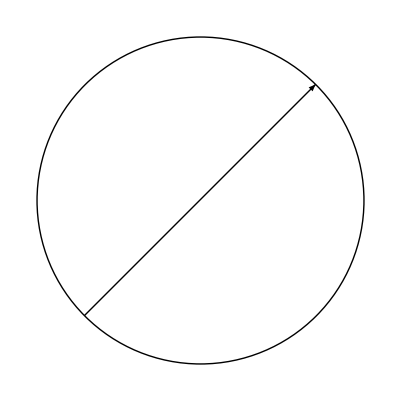

```mathematica
Graphics[{AnnotatedArrow[1/Sqrt[2]{-1,-1},1/Sqrt[2]{1,1},"d = 2"],Circle[]}]
```

```mathematica
r f[x k0/r,h h0,H h0,z h0]BesselJ[n,2Pi √2 x]m/.{r->10,x->20,h->1,z->2,H->4}//N
```

5.63845×10^-7

```mathematica
NIntegrate[1.402360785398249 BesselJ[1,2 π x] 1.402360785398249 x a4s[x 1.402360785398249,1 1,4 1,0.6141471000000001 1],{x,0,10}]
```

0.00211909

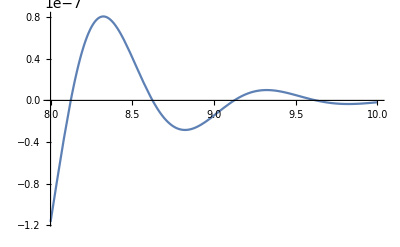

```mathematica
Plot[1.402360785398249 BesselJ[1,2 π x] 1.402360785398249 x a4s[x 1.402360785398249,1 1,4 1,0.6141471000000001 1],{x,8,10},PlotRange->All]
```

```mathematica
xx[]With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=xn √(r1^2+r2^2)},NIntegrate[k BesselJ[0,2Pi x]a2[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]]
```

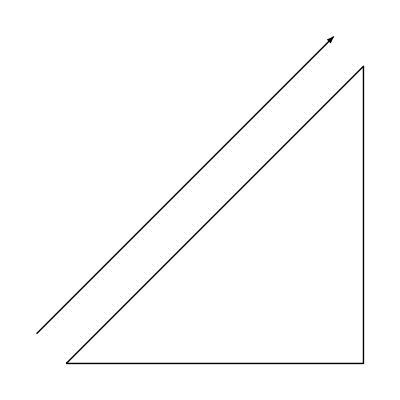

```mathematica
(*arallelDim[p_,q_,offset_,label_]:={Arrowheads[{{-.015,0.},{.015,0,Graphics[Line[{{0,1},{0,-1}}]]},{.015,1,Graphics[Line[{{0,1},{0,-1}}]]},{.015,1}}],Arrow[{p+offset,q+offset}]}*)
arallelDim[p_,q_,offset_,label_]:={Arrowheads[{{-.015,0.},{.015,0,Graphics[Line[{{0,1},{0,-1}}]]},{.015,1.0,Graphics[Line[{{0,1},{0,-1}}]]},{.015,1}}],Arrow[{p+offset,q+offset}]}
Graphics[{Thick,Line[{{0,0},{1,1},{1,0},{0,0}}],Thin,arallelDim[{0,0},{1,1},{-.1,.1},Sqrt[2]]}]
```

```mathematica
Div
```

```mathematica
Uncompressible
```

```mathematica
(* 函数定义区*)
```

```mathematica
j1xa1T[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=(2Pi)/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[1,  2Pi x]k x a1[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential" ]]];

j0x2a1T[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[0,2Pi x](k x)^2 a1[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]];
j0a2T[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[0,2Pi x]a2[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]];
j1xa4T[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h) },NIntegrate[k BesselJ[1,2Pi x] k x a4[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]];
(* For u13.*)

j1xa4sT[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[1,2Pi x] k x a4s[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]];
```

```mathematica
j0shT[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},If[x3<1.1h,j0shNhNearh[r1,r2,x3,h,H],With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=xn(√(r1^2+r2^2))/(x3-h)},NIntegrate[k BesselJ[0,2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]]];
```

```mathematica
(* 新老函数验证区.*)
```

```mathematica
j1xa1T[0.01,0.01,1,1,4]//AbsoluteTiming
```

{0.00907987,0.0024769}

```mathematica
j1xa1Nh[0.01,0.01,1,1,4]//AbsoluteTiming
```

Power::infy: 碰到无穷表达式 1/0.

{3.67626,0.0024769}

```mathematica
j0x2a1T[1,2,1,1,4]//AbsoluteTiming
```

{0.0397426,0.0789217}

```mathematica
j0x2a1Nh[1,2,1,1,4]//AbsoluteTiming
```

Power::infy: 碰到无穷表达式 1/0.

{0.345896,0.0789217}

```mathematica
j0a2T[1,2,1,1,4]//AbsoluteTiming
```

{0.0408731,-0.00299311}

```mathematica
j0a2Nh[1,2,1,1,4]//AbsoluteTiming
```

{0.296891,-0.00299311}

```mathematica
j1xa4T[1,2,1,1,4]//AbsoluteTiming
```

{0.0199105,-0.0429641}

```mathematica
j1xa4Nh[1,2,1,1,4]//AbsoluteTiming
```

Power::infy: 碰到无穷表达式 1/0.

{0.411256,-0.0429641}

```mathematica
j0shT[1,2,1.1,1,4]//AbsoluteTiming
```

{0.0849637,0.0515257}

```mathematica
j0shNh[1,2,1.1,1,4]//AbsoluteTiming
```

{0.267293,0.0515257}

```mathematica
(* 新老函数全局误差 沿 z 方向.*)
```

```mathematica
zz=Table[0.2*i,{i,1,20}];
zzh=Table[1+0.01*i,{i,0,30}];
```

```mathematica
j1xa1T[2,3,#,1,4]-j1xa1Nh[2,3,#,1,4]&/@zz
```

{-1.26832×10^-11,-7.77156×10^-16,-1.33227×10^-15,-1.38778×10^-15,-9.99201×10^-16,-1.16573×10^-15,-1.27676×10^-15,-1.02696×10^-15,-1.22125×10^-15,-1.13798×10^-15,-1.41553×10^-15,-1.30451×10^-15,-1.16573×10^-15,-1.19349×10^-15,-1.08247×10^-15,-6.93889×10^-16,-6.80012×10^-16,-5.55112×10^-16,-7.14706×10^-16,-1.70192×10^-16}

```mathematica
j0x2a1T[2,3,#,1,4]-j0x2a1Nh[2,3,#,1,4]&/@zz
```

{3.4469×10^-15,9.02056×10^-17,-2.01228×10^-16,-6.03684×10^-16,1.38778×10^-16,-6.93889×10^-17,-9.02056×10^-17,-1.52656×10^-16,-1.80411×10^-16,-1.31839×10^-16,1.04083×10^-16,-2.77556×10^-17,-6.93889×10^-17,-6.85563×10^-15,-7.35523×10^-15,-6.99441×10^-15,1.56125×10^-16,-3.1225×10^-17,2.01228×10^-16,8.95866×10^-17}

```mathematica
j0a2T[0.2,0.1,#,1,4]-j0a2Nh[0.2,0.1,#,1,4]&/@zz
```

{6.88338×10^-15,1.27676×10^-14,1.77636×10^-14,2.09832×10^-14,2.21767×10^-14,2.69409×10^-12,-1.19627×10^-14,-1.1352×10^-14,-9.10383×10^-15,-6.93889×10^-15,-4.78784×10^-15,-2.94209×10^-15,-1.40166×10^-15,1.249×10^-16,1.20737×10^-15,2.27596×10^-15,2.52576×10^-15,1.84922×10^-14,-7.94503×10^-16,-4.02174×10^-17}

```mathematica
j1xa4T[0.2,0.1,#,1.,4.]-j1xa4Nh[0.2,0.1,#,1.,4.]&/@zz
```

{1.19765×10^-14,1.67366×10^-14,1.58207×10^-14,-3.69843×10^-15,-1.31839×10^-15,8.26422×10^-15,1.21431×10^-16,-1.03979×10^-14,-1.09197×10^-13,-3.62557×10^-16,-7.07767×10^-16,-7.05165×10^-16,-4.02456×10^-16,6.37511×10^-17,4.571×10^-16,3.219×10^-16,-1.30104×10^-17,-3.51282×10^-17,-5.11093×10^-16,0.+NIntegrate[28.0993 BesselJ[1,2 π x] 28.0993 x a4[x 28.0993,1. 1,4. 1,4. 1],{x,0,0.402492},Method→DoubleExponential]}

```mathematica
j1xa4sT[0.2,0.1,#,1.,4.]-j1xa4sNh[0.2,0.1,#,1.,4.]&/@zz
```

{9.95294×10^-13,2.6229×10^-15,2.74086×10^-15,-2.85189×10^-15,1.33227×10^-15,-6.8695×10^-16,-1.23859×10^-15,-7.5287×10^-16,1.249×10^-16,9.15934×10^-16,5.11743×10^-16,3.92048×10^-16,3.8641×10^-16,3.53016×10^-16,4.58401×10^-16,1.43115×10^-16,-1.30972×10^-16,2.72699×10^-15,1.9906×10^-16,0.+NIntegrate[28.0993 BesselJ[1,2 π x] 28.0993 x a4s[x 28.0993,1. 1,4. 1,4. 1],{x,0,0.402492},Method→DoubleExponential]}

```mathematica
j0shT[0.2,0.1,#,1.,4.]-j0shNh[0.2,.1,#,1.,4.]&/@zzh//AbsoluteTiming
```

{11.1442,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-3.9968×10^-15,-1.11022×10^-15,-1.11022×10^-15,-2.22045×10^-16,-2.22045×10^-16,8.88178×10^-16,-2.22045×10^-16,2.22045×10^-16,8.88178×10^-16,8.88178×10^-16,4.44089×10^-16,6.66134×10^-16,4.44089×10^-16,4.44089×10^-16,6.66134×10^-16,4.44089×10^-16,-1.25489×10^-11,1.33227×10^-15,1.33227×10^-15,1.33227×10^-15,6.66134×10^-16}}

```mathematica
j0shT[3.,4.,#,1.,4.]-j0shNh[3.,4.,#,1.,4.]&/@zzh//AbsoluteTiming
```

{11.4184,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.50911×10^-11,1.00915×10^-10,1.00054×10^-10,9.4198×10^-11,8.48908×10^-11,7.34675×10^-11,6.10215×10^-11,4.84078×10^-11,3.62674×10^-11,2.50422×10^-11,1.50129×10^-11,6.33951×10^-12,-9.26924×10^-13,-6.81279×10^-12,-1.13896×10^-11,-1.47754×10^-11,-1.71013×10^-11,-1.85093×10^-11,-1.91432×10^-11,-1.915×10^-11,-1.86506×10^-11}}

```mathematica
j1xshNh[3.,4.,#,1.,4.]-j1xshNhNearh[3.,4.,#,1.,4.]&/@zzh//AbsoluteTiming
```

Power::infy: 碰到无穷表达式 1/0..

NIntegrate::nconv: 振荡积分可能不是收敛的.

General::stop: 在本次计算中，NIntegrate::nconv 的进一步输出将被抑制.

{13.3495,{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.81878×10^-10,7.47258×10^-10,6.1267×10^-10,4.84091×10^-10,3.65548×10^-10,2.59514×10^-10,1.67223×10^-10,8.89693×10^-11,2.44028×10^-11,-2.73322×10^-11,-6.73682×10^-11}}

```mathematica
j1xa4T[0.2,0.1,#,1,4]-j1xa4Nh[0.2,0.1,#,1,4]&/@zz
```

```mathematica
Log[10]//N
```

2.30259

```mathematica
a4[2 28.0992589241629,1. 1.,4. 1,4. 1]
```

0.

```mathematica
Simplify[(28.0992589241629 x (0.-449.5881427866064 x Sinh[84.2977767724887 x]+449.5881427866064 x (0.+1. Sinh[84.2977767724887 x])))/(-12633.093633394374 x^2+Sinh[112.3970356966516 x]^2)]
```

0.

```mathematica
u11Nh[4.18072045,1.61116966,#,1.,4.]&/@zzh
```

Power::infy: 碰到无穷表达式 1/0..

NIntegrate::nconv: 振荡积分可能不是收敛的.

General::stop: 在本次计算中，NIntegrate::nconv 的进一步输出将被抑制.

{0.0134608+3.90106 NIntegrate[1.40236 BesselJ[1,2 π x] 1.40236 x sh[x 1.40236,1. 1,4. 1,1. 1],{x,0,∞},Method→ExtrapolatingOscillatory],0.0316858,0.0318858,0.0320834,0.0322785,0.0324712,0.0326614,0.0328492,0.0330346,0.0332175,0.033398,0.0335761,0.0337517,0.0339249,0.0340957,0.034264,0.0344299,0.0345933,0.0347544,0.034913,0.0350691,0.0352228,0.0353742,0.035523,0.0356695,0.0358135,0.0359552,0.0360944,0.0362312,0.0363655,0.0364975}

```mathematica
v11Nh[4.18072045,1.61116966,#,1.,4.]&/@zzh
```

Power::infy: 碰到无穷表达式 1/0..

NIntegrate::nconv: 振荡积分可能不是收敛的.

{0.00500212+3.90106 NIntegrate[1.40236 BesselJ[1,2 π x] 1.40236 x sh[x 1.40236,1. 1,4. 1,1. 1],{x,0,∞},Method→ExtrapolatingOscillatory],0.0231917,0.0233571,0.0235207,0.0236826,0.0238426,0.0240009,0.0241575,0.0243122,0.0244652,0.0246164,0.0247657,0.0249132,0.025059,0.0252028,0.0253449,0.0254851,0.0256234,0.0257599,0.0258945,0.0260272,0.026158,0.026287,0.026414,0.0265392,0.0266625,0.0267838,0.0269032,0.0270207,0.0271363,0.0272499}

```mathematica
v11Nh[4.18072045,16.1116966,1.0,1.,4.]
```

Power::infy: 碰到无穷表达式 1/0..

NIntegrate::nconv: 振荡积分可能不是收敛的.

1.80385×10^-7+1.05005 NIntegrate[0.377476 BesselJ[1,2 π x] 0.377476 x sh[x 0.377476,1. 1,4. 1,1. 1],{x,0,∞},Method→ExtrapolatingOscillatory]

```mathematica
j0shNh[4.18072045,16.1116966,1.2,1.,4.]
```

2.06383×10^-7

```mathematica
k BesselJ[0,2Pi*x]sh[x k,h h0,H h0,x3 h0]/.{r1->4.18072045, r2->1.61116966,k->2 Pi/(√(4.18072045^2+1.61116966^2)),h->1,H->4,x3->1.2,x->0.1}//N
```

0.121572

```mathematica
xn(√(r1^2+r2^2))/(x3-h)/.{r1->4.18072045, r2->1.61116966,h->1,x3->1.2}
```

201.62

```mathematica
(750*25+250*4.5)/3600
```

5.52083